```mathematica
pot[x_]:=(x^2-4)^2/10
-pot'[x]
```

-2/5 x (-4+x^2)

```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
(* f[x_] := Sin[x] *)
(* f[{x_,y_}]:={y,-Sin[x]}; *)
f[{x_,y_}]:={y,-pot'[x]}
(* constant diffusion *)
g=0.1;
```

```mathematica
(* phase plot for deterministic system *)
```

```mathematica
gettraj[i_]:=Block[
{mysol},mysol=NDSolve[{{x'[t],y'[t]}==f[{x[t],y[t]}],{x[0],y[0]}==ic[[i]]},{x[t],y[t]},{t,0,16π},PrecisionGoal->16];
ParametricPlot[{x[t],y[t]}/.mysol,{t,0,16π},PlotRange->{{-4,4},{-4,4}}]
]
```

```mathematica
numtraj=7;
ic=Table[{-2 + (i-1) 4/(numtraj-1),-2.0+4 (j-1)/(numtraj-1)},{i,1,numtraj},{j,1,numtraj}];
ic=Flatten[ic,1];
nic=Length[ic];
```

```mathematica
trajectories=Table[gettraj[i],{i,1,nic}];
```

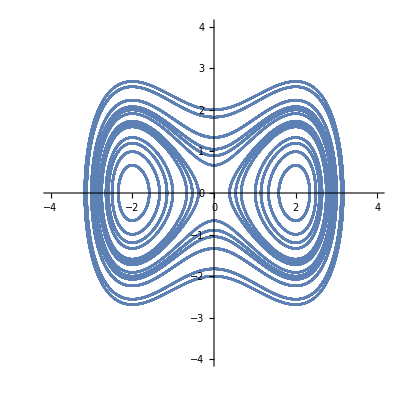

```mathematica
phaseplot=Show[trajectories]
```

```mathematica
cf=Compile[{{x,_Real,1}},f[x]]
```

CompiledFunction[…]

```mathematica
ntraj=100;
nsamp=1;
(* plots=Table[{},{i,ntraj}]; *)
dt = 0.0001;
ns = 400000;
tvec=Table[j*dt,{j,0,ns}];
For[traj=1,traj≤ntraj,traj+=1,
mcsol=Table[{0,0},ns+1];
ic={RandomVariate[NormalDistribution[0,1/3],1][[1]],0.0};
keepgoing=True;
While[keepgoing==True,
dlmat=Transpose[{RandomVariate[StableDistribution[1,α,0.0,0.0,(dt)^(1/α) g],ns],
RandomVariate[StableDistribution[1,α,0.0,0.0,(dt)^(1/α) g],ns]}];
keepgoing=Check[FoldList[#1 + dt cf[#1]+#2 &,ic,dlmat],True]];
Print[Max[Abs[keepgoing]]];
mcsol=keepgoing;
(*For[i=1,i≤ns,i+=1,mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  dlmat[[i]]);
]; *)
fname=StringJoin["mctrigdblwell2d",ToString[traj],".dat"];
myfile=OpenWrite[fname,BinaryFormat->True];
BinaryWrite[myfile,mcsol,"Real64"];
Close[myfile];Print[fname]
(* plots[[traj]]=ListPlot[mcsol]; *)
]
```

271.544

mctrigdblwell2d1.dat

81.3277

mctrigdblwell2d2.dat

98.2534

mctrigdblwell2d3.dat

31.1327

mctrigdblwell2d4.dat

16.4154

mctrigdblwell2d5.dat

83.8685

mctrigdblwell2d6.dat

19.3757

mctrigdblwell2d7.dat

12.5485

mctrigdblwell2d8.dat

2328.65

mctrigdblwell2d9.dat

31.2602

mctrigdblwell2d10.dat

13.1559

mctrigdblwell2d11.dat

481.538

mctrigdblwell2d12.dat

23.9259

mctrigdblwell2d13.dat

61.885

mctrigdblwell2d14.dat

58.7914

mctrigdblwell2d15.dat

672.387

mctrigdblwell2d16.dat

222.162

mctrigdblwell2d17.dat

272.207

mctrigdblwell2d18.dat

25.4902

mctrigdblwell2d19.dat

210.662

mctrigdblwell2d20.dat

75.4604

mctrigdblwell2d21.dat

253.258

mctrigdblwell2d22.dat

81.5077

mctrigdblwell2d23.dat

29.2799

mctrigdblwell2d24.dat

107.874

mctrigdblwell2d25.dat

349.324

mctrigdblwell2d26.dat

72.6446

mctrigdblwell2d27.dat

357.838

mctrigdblwell2d28.dat

265.242

mctrigdblwell2d29.dat

92.4013

mctrigdblwell2d30.dat

32.709

mctrigdblwell2d31.dat

162.642

mctrigdblwell2d32.dat

109.527

mctrigdblwell2d33.dat

43.1897

mctrigdblwell2d34.dat

38.0121

mctrigdblwell2d35.dat

135.262

mctrigdblwell2d36.dat

113.633

mctrigdblwell2d37.dat

128.914

mctrigdblwell2d38.dat

206.342

mctrigdblwell2d39.dat

31.7436

mctrigdblwell2d40.dat

283.752

mctrigdblwell2d41.dat

10.553

mctrigdblwell2d42.dat

138.937

mctrigdblwell2d43.dat

14.145

mctrigdblwell2d44.dat

44.3231

mctrigdblwell2d45.dat

37.9787

mctrigdblwell2d46.dat

49.7575

mctrigdblwell2d47.dat

96.4807

mctrigdblwell2d48.dat

145.641

mctrigdblwell2d49.dat

122.06

mctrigdblwell2d50.dat

39.296

mctrigdblwell2d51.dat

105.247

mctrigdblwell2d52.dat

54.8261

mctrigdblwell2d53.dat

23.1065

mctrigdblwell2d54.dat

41.4477

mctrigdblwell2d55.dat

11.2936

mctrigdblwell2d56.dat

85.5909

mctrigdblwell2d57.dat

24.8526

mctrigdblwell2d58.dat

151.1

mctrigdblwell2d59.dat

18.3057

mctrigdblwell2d60.dat

70.3143

mctrigdblwell2d61.dat

665.131

mctrigdblwell2d62.dat

40.3242

mctrigdblwell2d63.dat

103.056

mctrigdblwell2d64.dat

650.339

mctrigdblwell2d65.dat

289.821

mctrigdblwell2d66.dat

371.158

mctrigdblwell2d67.dat

61.8867

mctrigdblwell2d68.dat

71.4725

mctrigdblwell2d69.dat

56.0327

mctrigdblwell2d70.dat

104.571

mctrigdblwell2d71.dat

39.2656

mctrigdblwell2d72.dat

24.3026

mctrigdblwell2d73.dat

123.784

mctrigdblwell2d74.dat

55.009

mctrigdblwell2d75.dat

67.3246

mctrigdblwell2d76.dat

59.7943

mctrigdblwell2d77.dat

297.544

mctrigdblwell2d78.dat

28.577

mctrigdblwell2d79.dat

36.8352

mctrigdblwell2d80.dat

11.3054

mctrigdblwell2d81.dat

44.5324

mctrigdblwell2d82.dat

12.0354

mctrigdblwell2d83.dat

228.205

mctrigdblwell2d84.dat

528.564

mctrigdblwell2d85.dat

25.0368

mctrigdblwell2d86.dat

44.2667

mctrigdblwell2d87.dat

15.2108

mctrigdblwell2d88.dat

1335.37

mctrigdblwell2d89.dat

96.8278

mctrigdblwell2d90.dat

149.946

mctrigdblwell2d91.dat

680.656

mctrigdblwell2d92.dat

14.9313

mctrigdblwell2d93.dat

11.6482

mctrigdblwell2d94.dat

52.1808

mctrigdblwell2d95.dat

255.13

mctrigdblwell2d96.dat

75.3687

mctrigdblwell2d97.dat

272.513

mctrigdblwell2d98.dat

93.6561

mctrigdblwell2d99.dat

56.8445

mctrigdblwell2d100.dat